```mathematica
(* Simulation of Population distribution *)
DeathRate[n_,k_,m_,g_]:=((g n)^k/(( k)^k Exp[- k]))Exp[- g n]+m(g n-k)^2/k^2 UnitStep[-g n+k];
BirthRate[n_,BR_,BA_]:=Exp[-(n-BA)^2/(2 BR^2)];
```

```mathematica
A[1,0]=100;
Table[A[i,0]=0,{i,2,100}];
```

```mathematica
Array[A,100,100];Array[Pop,100];
```

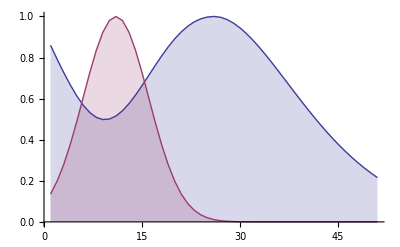

```mathematica
MLA=5;
BDR=0.86;
DR=0.2;
BR=5;
ACB=10;
DRlist=Table[DeathRate[i,MLA,BDR,DR],{i,0,50}];
BRList=Table[BirthRate[i,BR,ACB],{i,0,50}];
ListPlot[{DRlist,BRList},Filling ->Axis,Joined->True,PlotRange->All]
```

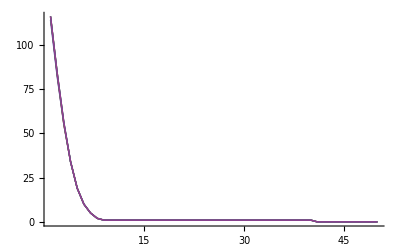

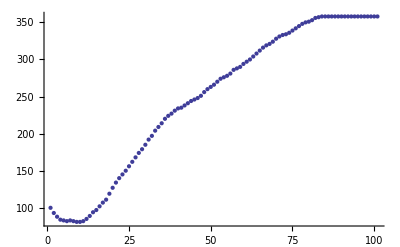

```mathematica
Do[
Do[
A[i,j]=Round[A[i-1,j-1]*DeathRate[i,MLA,BDR,DR]];
,{i,2,100}];
A[1,j]=Sum[Round[A[i,j-1] BirthRate[i,BR,ACB]],{i,1,100}];
,{j,1,100}]
Table[Pop[j]=Table[A[i,j],{i,1,50}],{j,0,100}];
ListPlot[Table[Pop[i],{i,80,85}],Joined->True,PlotRange->All]
ListPlot[Table[Tot[j]=Sum[A[i,j],{i,1,50}],{j,0,100}],PlotRange->{0,All}]
```